# Particle in a double-well potential, conservative system and homoclinic orbit

## Potential function

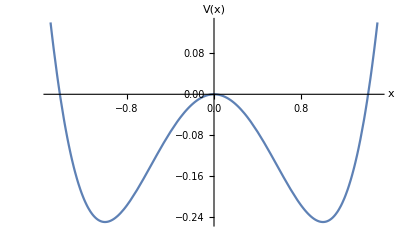

```mathematica
Plot[-1/2 x^2+1/4 x^4,{x,-1.5,1.5},AxesLabel->{x,V[x]},LabelStyle->20]
```

### Linear f.p.s and nonlinear phase portraits about their respective f.p.s

System

(y
x-x^3)

Jacobian matrix

(0 | 1
1-3 x^2 | 0)

Jacobian matric about f.p.s

{(0 | 1
-2 | 0),(0 | 1
1 | 0),(0 | 1
-2 | 0)}

Determinants

{2,-1,2}

Trace

{0,0,0}

Eigenvalues

{{ⅈ √2,-ⅈ √2},{-1,1},{ⅈ √2,-ⅈ √2}}

Eigenvektors

{{{-ⅈ/(√2),1},{ⅈ/(√2),1}},{{-1,1},{1,1}},{{-ⅈ/(√2),1},{ⅈ/(√2),1}}}

F.p.s coordinates

{{-1,0},{0,0},{1,0}}

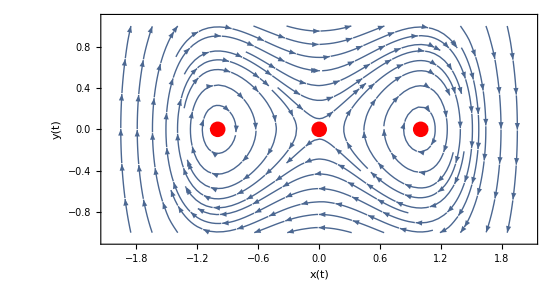
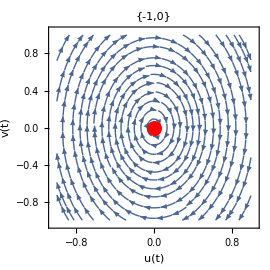
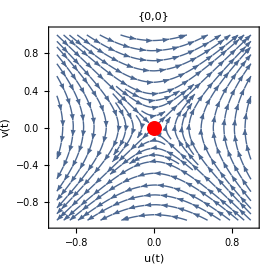
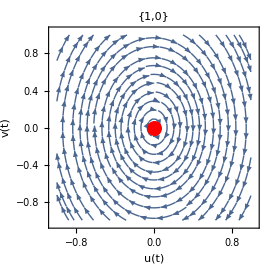
-Graphics- |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
Clear[diffX,diffY,x,y]
diffX=y;
diffY=x-x^3;
fixedpoints=Solve[{diffX==0,diffY==0},{x,y}];
a={diffX,diffY};
Print[Style["System",18,Blue]]
MatrixForm[a]
Print[Style["Jacobian matrix",18,Blue]]
D[a,{{x,y}}]//MatrixForm (*Jacobian*)
Jfp=D[a,{{x,y}}]/.fixedpoints ; (*linearised systems' matrices about f.p.s*)
Print[Style["Jacobian matric about f.p.s",18,Blue]]
Map[MatrixForm][Jfp]

Print[Style["Determinants",18,Blue]]
Map[Det][Jfp]
Print[Style["Trace",18,Blue]]
Map[Tr][Jfp]
Print[Style["Eigenvalues",18,Blue]]
Map[Eigenvalues][Jfp]
Print[Style["Eigenvektors",18,Blue]]
Map[Eigenvectors][Jfp]
Print[Style["F.p.s coordinates",18,Blue]]
coordinates={x,y}/.fixedpoints

fixedp=Graphics[{PointSize[0.02],Red,Point[coordinates]}];
fixedp0=Graphics[{PointSize[0.04],Red,Point[{0,0}]}];

sp=Show[StreamPlot[{diffX,diffY},{x,-2,2},{y,-1,1},FrameLabel->{x[t],y[t]},LabelStyle->18,ImageSize->560,AspectRatio->Automatic],fixedp];
spFP1=Show[StreamPlot[ Jfp[[1]].({{x}, {y}}),{x,-1,1},{y,-1,1},FrameLabel->{ u[t], v[t]},PlotLabel-> coordinates[[1]],LabelStyle->18,ImageSize->270],fixedp0];
spFP2=Show[StreamPlot[ Jfp[[2]].({{x}, {y}}),{x,-1,1},{y,-1,1},FrameLabel->{ u[t], v[t]},PlotLabel-> coordinates[[2]],LabelStyle->18,ImageSize->270],fixedp0];
spFP3=Show[StreamPlot[ Jfp[[3]].({{x}, {y}}),{x,-1,1},{y,-1,1},FrameLabel->{ u[t], v[t]},PlotLabel-> coordinates[[3]],LabelStyle->18,ImageSize->270],fixedp0];
Grid[{{sp,SpanFromLeft,SpanFromLeft},
{spFP1,spFP2,spFP3}},Frame->All]
```

## Numerical solution

```mathematica
Clear[diffX,diffY,x,y]
imagesize=350;maxT=25;

diffX=y;
diffY=x-x^3;
difX=y[t];
difY=x[t]-x[t]^3;
splot=StreamPlot[{diffX,diffY},{x,-2,2},{y,-2,2},FrameLabel->{x[t],y[t]},ImageSize->imagesize,LabelStyle->15];
fixedpoints=Solve[{diffX==0,diffY==0},{x,y}];
coordinates={x,y}/.fixedpoints;
fixedp=Graphics[{PointSize[0.03],Red,Point[coordinates]}];
Manipulate[
integration=NDSolve[{
x'[t]==difX,
y'[t]==difY,
x[0]==point[[1]],y[0]==point[[2]]},
{x,y},{t,0,T}];
trajectory=ParametricPlot[
Evaluate[{x[t],y[t]}/.integration],
{t,0,T},PlotStyle->Red];
solx=Plot[
Evaluate[x[t]/.integration],
{t,0,T},PlotRange-> All,AxesLabel-> {t,x[t]},ImageSize->imagesize,LabelStyle->15];
soly=Plot[
Evaluate[y[t]/.integration],
{t,0,T},PlotRange-> All,AxesLabel-> {t,y[t]},ImageSize->imagesize,LabelStyle->15];
Grid[{{Show[splot,trajectory,fixedp],soly},{solx}},Frame->All],
{{T,0.4 maxT,"Integration time, t"},1,maxT,Appearance->"Labeled"},
{{point,{1,1}},Locator}, 
SaveDefinitions->True,TrackedSymbols:>{T,point}]
```

## Hamiltonian

-Graphics3D-

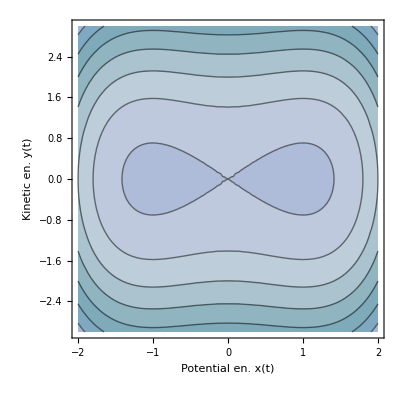

```mathematica
xdom=2;
ydom=3;
Allenergy=0.5 y^2-0.5 x^2+0.25 x^4;

Plot3D[Allenergy,
{x,-xdom,xdom},
{y,-ydom,ydom},
AxesLabel->{"Potential en." x[t],"Kinetic en." y[t],"Energy E(x,y)"},
ColorFunction->"Aquamarine",
MeshFunctions -> {#3&},
BoxRatios->{1,1,1},
PlotRange->{-0.25,2},ClippingStyle->None,LabelStyle->19]

ContourPlot[Allenergy,
{x,-xdom,xdom},
{y,-ydom,ydom},
ColorFunction->"Aquamarine",LabelStyle->16,
FrameLabel->{"Potential en." x[t],"Kinetic en." y[t]}]
```

Creation of this notebook was supported by IT Academy program of Information Technology Foundation for Education (HITSA).